```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
```

## Impulse in time from receiver

For the frequency given, we have mesh t ∈ Range[0, 6.59734,0.153427]

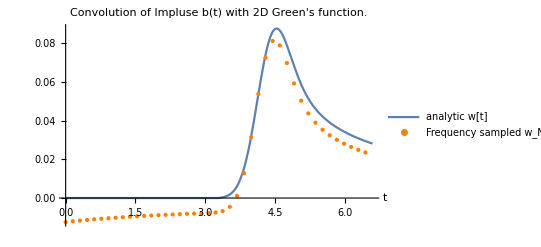

```mathematica
Do a convolution test before changing the impulse function;

	maxω=20.; 
	Nω= 21; 
         rngωFourier= rngωFourierOffset[maxω,Nω];
	b1[τ_]= ⅇ^(-5(τ-1)^2); (*impulses should be centred around t=0 for the multiple scattering code*)
	ConvolutionTest[b1, π Nω/maxω ,rngωFourier]
 (* Explanation:
Frequency sampled: first estimates the frequency of b1, then does a convolution in frequency space with the 2D Green's function, then inverts.
Analytic: does a convolution in time with b1 and with the 2D green's function in time.
*)
```

```mathematica
Xs={{2.0,0.}};
radius=1.0;
N0=4;

options={
"ImpulseFunction"->( ⅇ^(-5#^2)&),
"ImpulsePosition"-> {-1.,0.},
"MaxFrequencySamples"-> 45,
"PrintChecks"-> False,
"MaxFrequency"-> 10./radius,
"MaxTime"-> 10,
"MeshSize"->radius/3,
"BoundaryCondition"-> "Dirichlet",(*"BoundaryCondition"-> "Neumann",*)
"MaxTimeSamples"-> 2
(*,"MaxRadius"->3*)
};


{{{x0,x1},{y0,y1}},listWaves}= ListWavesDueToImpulse[Xs, radius,N0,options];
```

For the frequency given, we have mesh t ∈ Range[0, 28.2743,0.310707]

$Aborted

```mathematica
plotSequence= ListPlotSequence[listWaves,options];
listplots= (Show@@#)&/@Thread[{plotSequence,DrawScatterers[Xs,radius]}];
Export[NotebookDirectory[]<>"OneBigScatterer.gif",listplots]
```

/home/art/uom/study/Scattering/ScatterCylinder/v3/examples/OneBigScatterer.gif